```mathematica
Solve[x^2(x^6+x^3-1)==0, x, Reals]
```

{{x→0},{x→0},{x→Root-1.17Root[-1+#1^3+#1^6&,1]-1.1739849967053284},{x→Root0.852Root[-1+#1^3+#1^6&,2]0.851799642079243}}

```mathematica
1-1/4
```

3/4

```mathematica
D[x^2(x^6+x^3-1),x]
```

```mathematica
x^2 (3 x^2+6 x^5)+2 x (-1+x^3+x^6) /. {x-> (1/2 (-1+√5))^(1/3)} // N
```

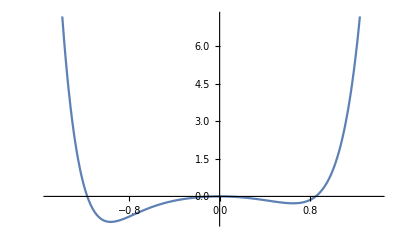

```mathematica
Plot[x^2(x^6+x^3-1), {x, -1.5, 1.4}]
```

```mathematica
Solve[Exp[-x]-Tanh[x] ==0, x]
```

{{x→ConditionalExpression[2 ⅈ π C[1]+Log[Root1.84Root[-1-#1-#1^2+#1^3&,1]1.8392867552141612], C[1]∈ℤ]},{x→ConditionalExpression[2 ⅈ π C[1]+Log[Root-0.420-0.606 ⅈRoot[-1-#1-#1^2+#1^3&,2]-0.4196433776070806], C[1]∈ℤ]},{x→ConditionalExpression[2 ⅈ π C[1]+Log[Root-0.420+0.606 ⅈRoot[-1-#1-#1^2+#1^3&,3]-0.4196433776070806], C[1]∈ℤ]}}

```mathematica
Series[Tanh[x], {x, 0, 3}]
```

x-x^3/3+O[x]^4

```mathematica
-(1/6)+ + (1/3)
```

1/6

```mathematica
D[Exp[-x]-Tanh[x], x] /. {x-> }
```

-ⅇ^-x-Sech[x]^2

```mathematica
Solve[1-2 x+x^2/2==0, x] // N
```

{{x→0.585786},{x→3.41421}}

```mathematica
Series[Sin[x], {x, 0,3}]
```

x-x^3/6+O[x]^4

```mathematica
Series[Tanh[x], {x, 0, 3}]
```

x-x^3/3+O[x]^4

```mathematica
Series[Sin[x], {x, 0, 7}] - Series[Tanh[x], {x, 0, 7}] // Normal
```

```mathematica
Solve[x^3/6-x^5/8+(271 x^7)/5040==0, x, Reals]
```

{{x→0},{x→0},{x→0}}

```mathematica
D[Sin[x]-Tanh[x], x] /. {x-> -1.8751}
```

-0.389409

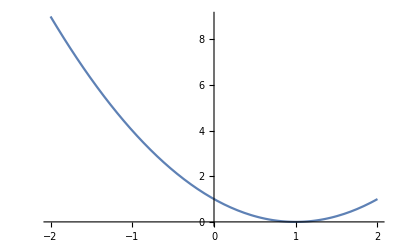

```mathematica
Plot[(x-1)^2, {x, -2, 2}]
```

```mathematica
f[x_, r_]:= x(1+r x + x^2)
```

```mathematica
Solve[f[x, r] == 0 && D[f[x, r], x] == 0, {x, r}]
```

{{x→-1,r→2},{x→1,r→-2}}

```mathematica
D[f[x, r], x] // Simplify
```

1+2 r x+3 x^2

```mathematica
Series[f[x, r], {x, -1, 2}, {r, 2, 1}]//Normal
```

-2+r-2 (-2+r) (1+x)+(-3+r) (1+x)^2

```mathematica
<<
```

```mathematica
D[f[x, r], x] // Simplify /.{x-> (-r-√(r^2-4))/2}
```

```mathematica
1+2 r x+3 x^2/.{x-> (-r+√(r^2-4))/2} // Simplify
```

1/2 (-4+r^2-r √(-4+r^2))

```mathematica
ClearAll[f]
```

```mathematica
f[x_, r_]:= x(1+r x - x^2)
```

```mathematica
Solve[f[x, r]==0, x]
```

{{x→0},{x→1/2 (r-√(4+r^2))},{x→1/2 (r+√(4+r^2))}}

```mathematica
1/2 (r+√(4+r^2)) /. {r-> -2} // N
```

0.414214

```mathematica
D[f[x,r], x] /. {x-> 1/2 (r-√(4+r^2))} // Simplify
```

1/2 (-4-r^2+r √(4+r^2))

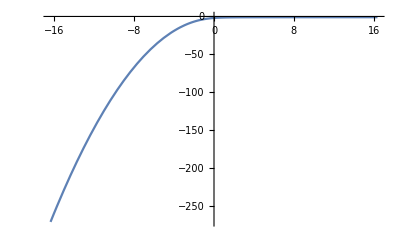

```mathematica
Plot[1/2 (-4-r^2+r √(4+r^2)),{r,-16.38,16.38}]
```

```mathematica
Solve[x(1-2y)==0 && -y(1-x)==0, {x, y}]
```

{{x→0,y→0},{x→1,y→1/2}}

```mathematica
Eigenvalues[{{0,-2}, {1/2, 0}}]
```

{ⅈ,-ⅈ}

```mathematica
Eigenvalues[{{1, 0}, {0, -1}}]
```

{-1,1}

```mathematica
ClearAll[f]
```

```mathematica
Grad[g[x, y], {x, y}] /. {x->0, y-> 0}
```

{3,1}

```mathematica
Grad[g[x, y], {x, y}] // Simplify
```

{3-6 x (-1+y),1-3 x^2-3 y^2}

```mathematica
f[x_, y_]:= x(1-3 x^2-y^2)-y(1+x)
g[x_, y_]:= y(1-3 x^2-y^2)+3x(1+x)
Solve[f[x, y]==0 && g[x, y]==0, {x, y},Reals]
```

{{x→0,y→0}}

```mathematica
val =2(1-3 x^2-y^2)(-2y) g[x, y]+ 2(1-3 x^2-y^2)(-6x) f[x,y]
```

-12 x (1-3 x^2-y^2) (-((1+x) y)+x (1-3 x^2-y^2))-4 y (1-3 x^2-y^2) (3 x (1+x)+y (1-3 x^2-y^2))

```mathematica
Collect[val, 1-3 x^2-y^2]
```

(-12 x^2-4 y^2) (1-3 x^2-y^2)^2

```mathematica
system = (-12 x^2-4 y^2) (1-3 x^2-y^2)^2
```

(-12 x^2-4 y^2) (1-3 x^2-y^2)^2

```mathematica
system /. {x-> r Cos[θ], y-> r Sin[θ]} // FullSimplify
```

-4 r^2 (2+Cos[2 θ]) (-1+2 r^2+r^2 Cos[2 θ])^2

```mathematica
g[x, y]/. {x-> r Cos[θ], y-> r Sin[θ]} // Simplify
```

3 r Cos[θ] (1+r Cos[θ])-r (-1+2 r^2+r^2 Cos[2 θ]) Sin[θ]

```mathematica
(x f[x, y] + y g[x, y])
```

x (-((1+x) y)+x (1-3 x^2-y^2))+y (3 x (1+x)+y (1-3 x^2-y^2))

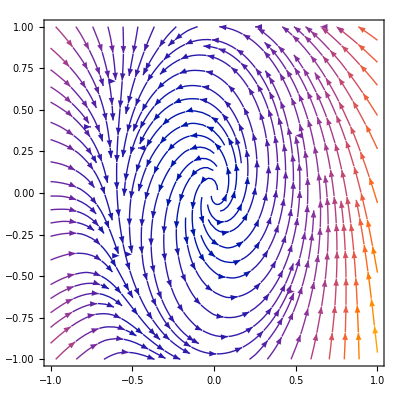

```mathematica
StreamPlot[{f[x,y], g[x, y]}, {x, -1, 1}, {y, -1, 1}]
```